# Génération de nombres aléatoires

## Générateur linéaire congruentiel

Le générateur linéaire congruentiel utilise le fait que G = {1, 2, 3, ..., n-1} avec la multiplication mod n est un groupe cyclique lorsque n est un nombre premier.

```mathematica
(* On choisit un nombre premier *)
n=2^31-1;PrimeQ[n]
```

True

```mathematica
(* On choisit une racine primitive *)
g=16807;

(* on choisit une valeur initiale qu'on appelle la semence (seed) *)
s=Mod[UnixTime[], n-1];
précédent=s;
```

```mathematica
(* La fonction (Nombre aléatoire) multiplie précédent par g, modulo n, puis renvoie le résultat. *)
GenerateurAléatoireCongruentiel[]:=(précédent=Mod[précédent g, n]);
```

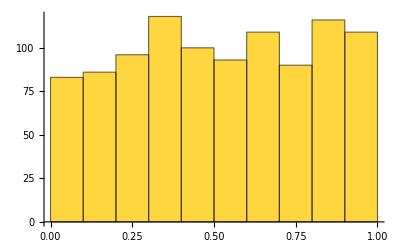

```mathematica
(* On peut appeler la fonction plusieurs fois de suite. On divise par n-1 pour avoir des nombres aléatoires entre 0 et 1 : *)
aléatoires=Table[GenerateurAléatoireCongruentiel[],{i, 1, 1000}];
Histogram[aléatoires/(n-1)]
```

## Le registre à décalage et les générateurs linéaires

On définit une récurrence linéaire (mod 2) avec la matrice A qui décale les bits et les combine pour obtenir le bit suivant. (Section 8.2)

```mathematica
q={1, 1, 0, 0}
r=Length[q];
MatrixForm[
A =Append[IdentityMatrix[r][[2;;r]], q]
]
```

{1,1,0,0}

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 1 | 0 | 0)

La suite est générée en considérant les vecteurs x_(n+1) = A x_n, et la sortie y_n=B x_n. Par exemple, si on veut récupérer le premier bit, on prend B = (1, 0, ...., 0);

```mathematica
MatrixForm[
B={IdentityMatrix[r][[1]]}
]
```

(1 | 0 | 0 | 0)

On initialise le registre à décalage avec une séquence initiale de r bits :

```mathematica
x=xInit=IdentityMatrix[r][[r]]
```

{0,0,0,1}

On peut alors générer toute la séquence  :

```mathematica
(* On génère toute la séquence jusqu'à ce qu'elle se répète. *)
séquence=Mod[B.xInit, 2];
While[(x=Mod[A.x, 2])!=xInit,
y=Mod[B.x, 2];
séquence=Join[séquence, y]
]
séquence
```

{0,0,0,1,0,0,1,1,0,1,0,1,1,1,1}

On peut comparer la longueur de la séquence  pour voir si elle est maximale.

```mathematica
l=Length[séquence]
l==2^r-1
```

15

True

On peut comparer la séquence à une version « décalée » de celle-ci, pour vérifier la corrélation -- c’est à dire la différence entre le nombre de bits qui sont égaux et le nombre de bits qui sont différents.

```mathematica
(* Fonction pour décaler périodiquement une séquence *)
PermutationPériodique[liste_, d_]:=
Join[liste[[Mod[d, Length[liste]]+1;;Length[liste]]], liste[[1;;Mod[d, Length[liste]]]]];

(* Fonction qui calcule la corrélation entre deux listes *)
Corrélation[liste1_, liste2_]:=((-1)^liste1).(-1)^liste2;

(* On affiche tous les décalages de la séquence *)
Grid[Join[
{{"Séquence décalée","Corrélation"}},
Table[
{(séquenceDécalée[i]=PermutationPériodique[séquence, i])[[1;;]],Corrélation[séquence, séquenceDécalée[i]]},
{i, 0, l-1}]
]]
```

Séquence décalée | Corrélation
{0,0,0,1,0,0,1,1,0,1,0,1,1,1,1} | 15
{0,0,1,0,0,1,1,0,1,0,1,1,1,1,0} | -1
{0,1,0,0,1,1,0,1,0,1,1,1,1,0,0} | -1
{1,0,0,1,1,0,1,0,1,1,1,1,0,0,0} | -1
{0,0,1,1,0,1,0,1,1,1,1,0,0,0,1} | -1
{0,1,1,0,1,0,1,1,1,1,0,0,0,1,0} | -1
{1,1,0,1,0,1,1,1,1,0,0,0,1,0,0} | -1
{1,0,1,0,1,1,1,1,0,0,0,1,0,0,1} | -1
{0,1,0,1,1,1,1,0,0,0,1,0,0,1,1} | -1
{1,0,1,1,1,1,0,0,0,1,0,0,1,1,0} | -1
{0,1,1,1,1,0,0,0,1,0,0,1,1,0,1} | -1
{1,1,1,1,0,0,0,1,0,0,1,1,0,1,0} | -1
{1,1,1,0,0,0,1,0,0,1,1,0,1,0,1} | -1
{1,1,0,0,0,1,0,0,1,1,0,1,0,1,1} | -1
{1,0,0,0,1,0,0,1,1,0,1,0,1,1,1} | -1

On peut analyser les fréquences pour les différentes suites de bits :

{0,1,2,4,1,3,6,5,2,5,3,7,7,6,4}

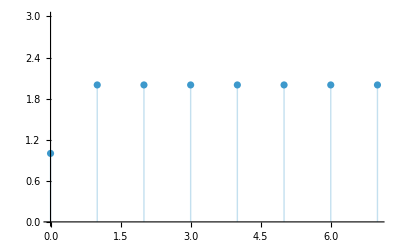

```mathematica
nbits=3;
nombres=Table[
FromDigits[séquenceDécalée[i][[1;;nbits]], 2],{i, 0, l-1}
]
ListPlot[t=Tally[nombres], Filling->Axis, PlotRange->{0, Max[t[[;;,2]]+1]}]
```